```mathematica
(
simple=Sort/@RandomReal[1,{10^6,4}];
max=Max@Differences@Join[{0},#,{1}]&;
data=ParallelMap[max,simple];
)//TS
```

Calls | Time | Evaluation
1 | 6.641 | simple=Sort/@RandomReal[1,{«2»}];max=Max[Differences[«1»]]&;data=ParallelMap[max,simple];
1 | 6.344 | data=ParallelMap[max,simple]
1 | 6.344 | ParallelMap[max,simple]
1 | 0.297 | simple=Sort/@RandomReal[1,{Power[«2»],4}]
1 | 0.297 | Sort/@RandomReal[1,{10^6,4}]
1 | 0.047 | RandomReal[1,{10^6,4}]

总运行时:  0.129558

CPU 时间:  0.0625

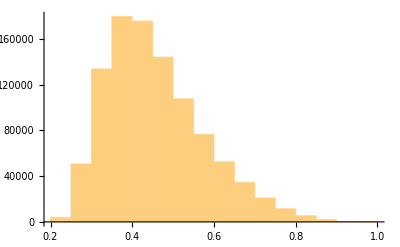

```mathematica
Histogram[data]//TT
```

```mathematica
FindDistribution[data]
```

MixtureDistribution[{0.639823,0.360177},{BetaDistribution[18.7922,28.4302],LogNormalDistribution[-0.568674,0.174084]}]

```mathematica
data//Mean
```

0.45661

```mathematica
Quit
```

```mathematica
Length@Select[data,#>0.25&]/10.^6//TT
```

All Time:  1.6573

CPU Time:  1.65625

0.996197

```mathematica
255/256//N
```

0.996094

```mathematica
data=With[{n=10^6},
simple=Sort/@RandomReal[1,{n,4}];
Max/@Differences[ArrayFlatten[{{0,simple,1}}],{0,1}]
];//TS
```

Calls | Time | Evaluation
1 | 2.11 | data=With[{Set[«2»]},Set[«2»];Map[«2»]];
1 | 2.11 | data=With[{n=Power[«2»]},simple=Map[«2»];Max/@Differences[«2»]]
1 | 2.11 | With[{n=10^6},simple=Sort/@RandomReal[«2»];Max/@Differences[ArrayFlatten[«1»],{«2»}]]
1 | 2.11 | simple=Sort/@RandomReal[1,{«2»}];Max/@Differences[ArrayFlatten[{«1»}],{0,1}]
1 | 1.781 | Max/@Differences[ArrayFlatten[{{«3»}}],{0,1}]
1 | 1.468 | Differences[ArrayFlatten[{{0,simple,1}}],{0,1}]
1 | 1.078 | ArrayFlatten[{{0,simple,1}}]
1 | 0.329 | simple=Sort/@RandomReal[1,{n,4}]
1 | 0.329 | Sort/@RandomReal[1,{n,4}]
1 | 0.063 | RandomReal[1,{n,4}]

```mathematica
SetOptions[$FrontEnd,StyleHints->{"CodeFont"->"等线"}]
```